# Teoria

## GF(2^m)

Formado com base em um p(x) primitivo

```mathematica
m=3;
```

```mathematica
p=1+X+X^3;
```

```mathematica
subst=p-X^m;
```

```mathematica
substα=subst/.X->α;
```

```mathematica
n=2^m-1;
```

```mathematica
expansions["recalculate"];
```

Para definir um “field”

```mathematica
GF[mNovo_,poly_]/;Not[PrimitivePolynomialQ[poly,2]∧Exponent[poly,X]===mNovo]:=Throw["Inconsistent GF call"]
```

```mathematica
GF[mNovo_,poly_]:=With[{},
m= mNovo;
p=poly;
subst=p- X^m;
substα=subst/.X->α;
n=2^m-1;
expansions["recalculate"];
]
```

Cíclico na multiplicação (muito lento : desativado)

```mathematica
(* α/:α^(i_/;i>n-1||i<0):=α^Mod[i,n] *)
```

Expandível em somas/potência para potências  ≥ m

```mathematica
ExpandAsSum[poly_]:=Collect[
PolynomialMod[poly,2],
X,
PolynomialMod[#,2]&@If[Head[#]===Plus,ExpandAsSumHelper/@#,ExpandAsSumHelper@# ]&
]
```

```mathematica
ExpandAsPower[poly_]:=Collect[
poly,
X,
ExpandAsPowerHelper@*ExpandAsSum
]
```

```mathematica
expansions["recalculate"]:=With[{},
ClearAll[ExpandAsSumHelper];
ClearAll[ExpandAsPowerHelper];
ExpandAsSumHelper[0]=0;
ExpandAsPowerHelper[0]=0;
Scan[
With[{
sumExpansion=PolynomialMod[#,2]&[#//.{α^i_/;i≥m+1:> Expand[α ExpandAsSumHelper[α^(i-1)]],α^m->substα}]
},
ExpandAsSumHelper[#]=sumExpansion;
ExpandAsPowerHelper[sumExpansion]=#;
]&,
Table[α^i,{i,0,n-1}]
];
ExpandAsSumHelper[α^i_]:=ExpandAsSumHelper[α^Mod[i,n]];
]
```

Conjugados de β são os β^(2j)

```mathematica
Conjugates[β_]:=α^#&/@NestWhile[#~Append~Mod[2 Last@#,n]&,{Exponent[ExpandAsPower@β,α]},!Mod[2 Last@#,n]∈#&]
```

Cada elemento tem um polinômio mínimo

```mathematica
MinPoly[β_]:=ExpandAsSum[Times@@Map[X+#&,Conjugates[β]]]
```

Raízes de polinômio por inspeção

```mathematica
PolyRoots[poly_]:=First[#,{}]&@Last@Reap@With[{deg=Exponent[poly,X]},
PolyRoots[]["count"]=0;
If[(poly/.X->0)~GFEqualsQ~0,Sow[0];PolyRoots[]["count"]=1];
NestWhile[
With[{},
If[(poly/.X->#)~GFEqualsQ~0,
Sow[#];
PolyRoots[]["count"]=PolyRoots[]["count"]+1;
];
# α
]&,
1,
PolyRoots[]["count"]<deg∧Exponent[#,α]<n&
];
];
```

Comparação robusta

```mathematica
GFEqualsQ[a_,b_]:=ExpandAsSum[a-b]===0
```

Inversão é um problema

```mathematica
Invert[β_]:=α^(n-Exponent[ExpandAsPower@β,α])
```

```mathematica
Invert[1]=1;
```

## BCH

Gerador do código

```mathematica
Generator::usage="Generator[t] assumes GF[m,poly] has been called beforehand";
```

```mathematica
Generator[t_]:=PolynomialLCM[Sequence@@Table[MinPoly[α^i],{i,1,2t-1,2}]]
```

```mathematica
Generator[t_/;t≥ 2^(m-1)]:=Throw["Inconsistent Generator call"]
```

Síndrome

```mathematica
Sindrome[codepoly_,t_]:=Table[ExpandAsPower[codepoly/.X->α^i],{i,1,2t}]
```

Decodificação

### Versão falha

```mathematica
discrepancy[σ_,S_,μ_]:=(S⟦μ+2⟧-1)+(σ/.{X^i_:>S⟦μ+2-i⟧}/.{X->S⟦μ+1⟧})
```

```mathematica
row[μ_,σ_,dμ_,lμ_]//{#["μ"]:=μ,#["σ"]:=σ,#["dμ"]:=dμ,#["lμ"]:=lμ,#["μ-lμ"]:=μ-lμ}&;
```

```mathematica
disassemble=#/@{"μ","σ","dμ","lμ"}&;
```

```mathematica
best=Last@*MaximalBy[#["μ-lμ"]&]@*Select[Not[#["dμ"]===0]&];
```

```mathematica
Decode[codepoly_,gen_,t_]:=Block[{sindrome=Sindrome[codepoly,t]},NestWhile[
#~Append~Block[{μ,σμ,dμ,lμ,ρ,σρ,dρ,lρ,σμ1,lμ1},
{μ,σμ,dμ,lμ}=disassemble@Last@#;
If[Not[dμ===0],
{ρ,σρ,dρ,lρ}=disassemble@best@Most@#;
σμ1=σμ+dμ Invert[dρ] X^(μ-ρ)σρ;
lμ1=Exponent[σμ1,X],

σμ1=σμ;
lμ1=lμ;
];
Echo@row[
μ+1,
ExpandAsPower@σμ1,
ExpandAsPower@discrepancy[σμ1,sindrome,μ],
lμ1
]
] &,
{row[-1,1,1,0],row[0,1,sindrome⟦1⟧,0]},
Length@#<2t+1&
] ]//Last//#["σ"]&//ExpandAsPower(*até expandir em potências*)//Echo//PolyRoots//Map[Invert]//ReplaceAll[α->X]//Apply[Plus]//(codepoly+#)&//PolynomialQuotient[#,gen,X]&//ExpandAsPower
```

### Versão funcional

```mathematica
Decode2[codepoly_,gen_,t_]:=Block[{
sindromePoly=Apply[Plus]@MapIndexed[#1 X^(#2⟦1⟧)&]@Sindrome[codepoly,t],
σ,τ,ω,γ,D,B,k,Δ
},
σ[0]=1;τ[0]=1;ω[0]=1;γ[0]=0;D[0]=0;B[0]=0;
k=0;
While[k<2t,
Δ[k]=ExpandAsPower@Coefficient[(1+sindromePoly)σ[k],X^(k+1)];
σ[k+1]=σ[k]-Δ[k] X τ[k];
ω[k+1]=ω[k]-Δ[k] X γ[k];
If[Δ[k]===0∨D[k]>(k+1)/2∨(Δ[k]=!=0∧D[k]===(k+1)/2∧B[k]===0),
D[k+1]=D[k];
B[k+1]=B[k];
τ[k+1]=X τ[k];
γ[k+1]=X γ[k],
D[k+1]=k+1-D[k];
B[k+1]=1-B[k];
τ[k+1]=Invert[Δ[k]]σ[k];
γ[k+1]=Invert[Δ[k]]ω[k];
];
k=k+1;
];
σ[2t]
]//PolyRoots//Map[Invert]//ReplaceAll[α->X]//Apply[Plus]//(codepoly+#)&//PolynomialQuotient[#,gen,X]&//ExpandAsPower
```

# Implementação

Testes

```mathematica
GF[5,1+X^2+X^5]
```

```mathematica
g=Generator[3]
```

(1+X^2+X^5) (1+X+X^2+X^4+X^5) (1+X^2+X^3+X^4+X^5)

```mathematica
Decode[g(1+X^2+X^3)+X^12+X^13+X^4,g,3]
```

1+X^2+X^3

```mathematica
g=Generator[3];
```

Berlekamp-Massey é linear no tamanho do código

Polinômios primitivos retirados <daqui>

```mathematica
polys={X^4+X^3+1,X^5+X^2+1,X^6+X+1,X^7+X+1,X^8+X^5+X^3+X+1,X^9+X^4+1,X^10+X^7+1,X^11+X^9+1,X^12+X^6+X^4+X+1,X^13+X^4+X^3+X+1,X^14+X^8+X^6+X+1,X^15+X+1};
```

```mathematica
Monitor[
times=Take[polys,8]//Map[Block[{curr=#},
GF[Exponent[#,X],#];
g=Generator[5];
AbsoluteTiming[Decode2[g(1+X^2+X^4)+X^12+X^13+X^4,g,5]]
]& ],
curr
]
```

{{0.014876,1+X^2+X^4},{0.014918,1+X^2+X^4},{0.020591,1+X^2+X^4},{0.02685,1+X^2+X^4},{0.061315,1+X^2+X^4},{0.08903,1+X^2+X^4},{0.164651,1+X^2+X^4},{0.310148,1+X^2+X^4}}

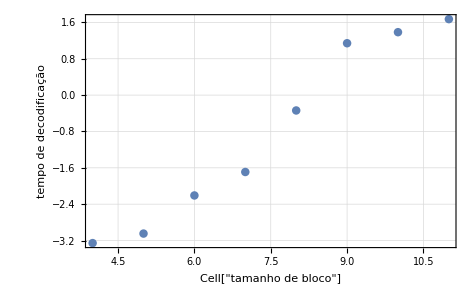

```mathematica
ListPlot[Transpose@{Range[4,Length@times+3],Map[Log@*First]@times},PlotTheme->"Detailed",FrameLabel->(Style[#,16]&/@{"Cell["tamanho de bloco",ExpressionUUID->"b2a24b25-6ae0-4879-a5c4-686f9a92dcbf"]","tempo de decodificação"}),FrameTicks->Automatic]
```

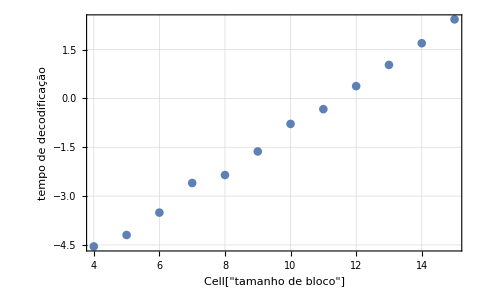

```mathematica
Exp[-0.26]
```

0.771052

Análise de desempenho (para tamanho de bloco pequeno)

### Exemplo que falhava em Decode original

```mathematica
GF[5,X^5+X^2+1]
```

```mathematica
g=Generator[5];
```

```mathematica
Decode2[g(X+X^2)+X+X^3+X^20,g,5]
```

X+X^2

```mathematica
Decode[g(X+X^2)+X+X^3+X^20,g,5]
```

row[1,1+X α^19,0,1]

row[2,1+X α^19,α^20,1]

row[3,1+X^2 α+X α^19,0,2]

row[4,1+X^2 α+X α^19,α^25,2]

row[5,1+X^2 α^11+X α^19+X^3 α^24,α^13,3]

row[6,1+X^2 α^17+X^3 α^30,α^30,3]

row[7,1+X^3 α^2+X^4 α^10+X α^17+X^2 α^28,α^19,4]

row[8,1+X^3 α^12+X α^15+X^4 α^26+X^2 α^28,α^12,4]

row[9,1+X+X^5 α^3+X^2 α^11+X^3 α^28,α^25,5]

1+X+X^5 α^3+X^2 α^11+X^3 α^28

1+X+X^2

### Preciso migrar para C++

```mathematica
GF[3,1+X+X^3]
```

```mathematica
g=Generator[2]
```

(1+X+X^3) (1+X^2+X^3)

```mathematica
ExpandAsSum@Sindrome[1+X,2]
```

{1+α,1+α^2,α,1+α+α^2}

```mathematica
polys={X^5+X^2+1,X^6+X+1,X^7+X+1,X^8+X^5+X^3+X+1,X^9+X^4+1,X^10+X^7+1,X^11+X^9+1,X^12+X^6+X^4+X+1,X^13+X^4+X^3+X+1,X^14+X^8+X^6+X+1,X^15+X+1};
```

```mathematica
GF[5,First@polys]
```

```mathematica
t=3;
g=Generator[t];
k=n-Exponent[g,X];
k/n//N
```

0.516129

```mathematica
4/7//N
```

0.571429